```mathematica
(*The purpose of this code is to solve for the 1D domain wall for Superconductivity. The calculations in this code are as follows. 
Section 1 - Solving the ODE numetically.
Here we just solve the G-L ODE numnerically. The domain has been approximated as [-L,L] so that we can take limits. The ODE is taken from ST. James and Sarma p 38/288.
We have also tried solving for f(x) if we assume h(x).
Section 2 - Here we try to solve the problem Variationally.  We use two choices of test functions
Choice 1 --> tanh for u and h
Choice 2 --> Only varies in a window [-l,l]  where it continuously interpolates between the bulk SC and bulk normal values.
*)
```

```mathematica
ClearAll["Global`*"]
```

## (*Solving the ODE numericaly*)

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
Needs["NDSolve`FEM`"]
```

```mathematica
κ=5;
L=10^4;
sml=0;
NDSolve[{-f[x]^3/κ^2*f''[x]+(h'[x])^2==f[x]^4-f[x]^6,f[x]^3*h[x]+2f'[x]*h'[x]+f[x]*h''[x]==0,f[-L]==sml,h[-L]==1/Sqrt[2],f[L]==1,h[L]==sml,},{f[x],h[x]},{x,-L,L}]
```

NDSolve::deqn: Equation or list of equations expected instead of Null in the first argument {h'[x]^2-1/25 f[x]^3 f''[x]==f[x]^4-f[x]^6,f[x]^3 h[x]+2 f'[x] h'[x]+f[x] h''[x]==0,f[-10000]==0,h[-10000]==1/(√2),f[10000]==1,h[10000]==0,Null}.

NDSolve[{h'[x]^2-1/25 f[x]^3 f''[x]==f[x]^4-f[x]^6,f[x]^3 h[x]+2 f'[x] h'[x]+f[x] h''[x]==0,f[-10000]==0,h[-10000]==1/(√2),f[10000]==1,h[10000]==0,Null},{f[x],h[x]},{x,-10000,10000}]

```mathematica
(*NDSolve[{-1/κ^2*f''[x]+1/f[x]^3(h'[x])^2==f[x]^1-f[x]^3,f[x]^2*h[x]+2/f[x]*f'[x]*h'[x]+1*h''[x]==0,f[-L]==sml,h[-L]==1/Sqrt[2],f[L]==1,h[L]==sml},{f[x],h[x]},{x,-L,L}]*)
```

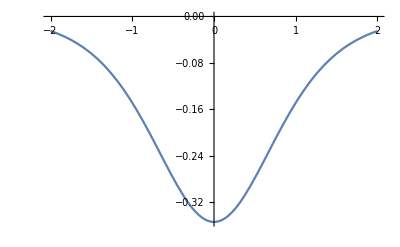

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == -8368.64551252846152783401892904.

{{f[x]→InterpolatingFunction[{{-10000.0000000000000000000000000, -8368.64551252846152783401892904}}, <>][x]}}

-Graphics-

```mathematica
h0[x_,a_]:=1/(2*Sqrt[2])*(Tanh[-x/a]-1)+1/Sqrt[2]
a0=1;
hp[x_]:=-Sech[x]^2/(2 √2)
Plot[hp[x],{x,-2,2}]
(*f[x]^3*h0[x,a0]+2f'[x]*D[h0[x,a0],x]+f[x]*D[h0[x,a0],{x,2}]==0
D[h0[x,a0],x]
s=NDSolve[{-1/κ^2*f''[x]+1/f[x]^3(-Sech[x]^2/(2 √2))^2==f[x]^1-f[x]^3,f[-L]==sml,f'[-L]==sml},{f[x]},{x,-L,L},Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->20]
Plot[Evaluate[f[x]/.s],{x,-L,L},PlotRange->All]*)
sol=NDSolve[{-f[x]^3/κ^2*f''[x]+(hp[x])^2==f[x]^4-f[x]^6,f[-L]==10^-4,f'[-L]==10^-6},{f[x]},{x,-L,L},MaxSteps->10000,PrecisionGoal->18,AccuracyGoal->18,WorkingPrecision->30,Method->"StiffnessSwitching"]
Plot[Evaluate[f[x]/. sol],{x,-L,L},PlotRange->All]
```

```mathematica
(*sol2=NDSolve[{-1/κ^2*u''[x]==u[x]^1-u[x]^3,u[1]==.5,u[L]==1},{u[x]},{x,1,L},MaxSteps->1000000,PrecisionGoal->18,AccuracyGoal->18,Method->"StiffnessSwitching"]
Plot[Evaluate[u[x]/. sol2],{x,1,L},PlotRange->All]*)
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InitializePDECoefficients::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

FindRoot::jsing1: Encountered a singular Jacobian at the point {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«72»}. Try perturbing the initial point(s).

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

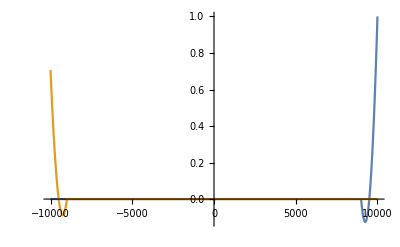

```mathematica
ic1=DirichletCondition[f[x]==0+sml,x==-L];
ic2=DirichletCondition[f[x]==1-sml,x==L];
ic3=DirichletCondition[h[x]==1/Sqrt[2]+sml,x==-L];
ic4=DirichletCondition[h[x]==sml,x==L];
ode1=-f[x]^3/κ^2*f''[x]+(h'[x])^2==f[x]^4-f[x]^6;
ode2=f[x]^3*h[x]+2f'[x]*h'[x]+f[x]*h''[x]==0;
sol3=NDSolve[{ode1,ode2,ic1,ic2,ic3,ic4},{f,h},{x,-L,L},Method->{"FiniteElement"}];
Plot[{Evaluate[f[x]/.sol3],Evaluate[h[x]/.sol3]},{x,-L,L},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
ic41={u[-L]==0+sml,u[L]==1-sml,A'[-L]==1/Sqrt[2],A[L]==1};
ode21=-1/κ^2*u''[x]+A[x]^2*u[x]==u[x]^1-u[x]^3;
ode22=u[x]^2*A[x]+A''[x]==0;
sol4=NDSolve[{ode21,ode22,ic41},{u,A},{x,-L,L},Method->{"FiniteElement"}];
Plot[{Evaluate[u[x]/.sol3],Evaluate[A[x]/.sol3]},{x,-L,L},AxesOrigin->{0,0},PlotRange->All]
```

NDSolve::fembderiv: The expression A'[-10000]==1/(√2) given as a spatial boundary condition for the possibly automatically chosen finite element method should not have explicit derivatives of the dependent variables. NeumannValue should be used to specify spatial derivatives at the boundary.

-Graphics-

```mathematica
(*Solving the ODE Variationally*)
```

```mathematica
(*The idea is to do a variational minimization. We fix the parameters and *)
GL1[u_,v_,A_,B_,H_] :=1/2*(1-u^2)^2(*here v is \nabla u,B=\curl A*)
GL2[u_,v_,A_,B_,H_] :=1/κ^2*v^2(*here v is \nabla u,B=\curl A*)
GL3[u_,v_,A_,B_,H_] :=u^2*A^2(*here v is \nabla u,B=\curl A*)
GL4[u_,v_,A_,B_,H_] :=(B-H)^2(*here v is \nabla u,B=\curl A*)
GL[u_,v_,A_,B_,H_] :=GL1[u,v,A,B,H]+GL2[u,v,A,B,H]+GL3[u,v,A,B,H]+GL4[u,v,A,B,H] (*here v is \nabla u, B=\curl A*)
```

### (*Test Function 1 - *)

```mathematica
u1[x_,ξ_,λ_,H_]:=1/2*(Tanh[x/ξ]+1)
A1[x_,ξ_,λ_,H_]:=H/2*(x-λ*Log[Cosh[x/λ]])
Hc=1/Sqrt[2];
D[u1[x,ξ,λ,Hc],x]
D[A1[x,ξ,λ,Hc],x]
(*The following is the expression for the Surface energy, ie, Energy of mixed state - Energy of pure normal state. It turns out to be 1/2.*)
Manipulate[NIntegrate[GL[1/2*(Tanh[x/ξ]+1),Sech[x/ξ]^2/(2 ξ),Hc/2*(x-λ*Log[Cosh[x/λ]]),1/2 Hc (1-Tanh[x/λ]),Hc]-1/2,{x,-L2,L2}],{L2,0.1,10^5},{ξ,0.1,10^3},{λ,0.1,10^3}]
```

Sech[x/ξ]^2/(2 ξ)

(1-Tanh[x/λ])/(2 √2)

```mathematica
(*The following is GL1[u1,A1]*)
Assuming[ξ>0&&L1>0,Integrate[1/2*(1-u1[x,ξ,λ,H]^2)^2,{x,-L1,L1}]]//Simplify
(*The following is GL2[u1,A1]*)
Assuming[ξ>0&&L1>0&&κ1>0,Integrate[1/κ1^2*Sech[x/ξ]^2/(2 ξ),{x,-L1,L1}]]//Simplify
(*The following is GL4[u1,A1]*)
Print["(∫^L1)_-L1(H/2*(1-Tanh[x/λ])-H)^2dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,Integrate[(H/2*(1-Tanh[x/λ])-H)^2,{x,-L1,L1}]]//Simplify]
```

1/2 (L1-1/24 ξ Tanh[L1/ξ] (-3+Tanh[L1/ξ]^2))

Tanh[L1/ξ]/κ1^2

(∫^L1)_-L1(H/2*(1-Tanh[x/λ])-H)^2dx=  1/2 H^2 (2 L1-λ Tanh[L1/λ])

```mathematica
(*The following are terms in GL3[u1,A1]. We expand each term as in the notes "OneNote(UH)/superConductivity/1D domain walls/ tanh as test function."*)
Print["(Tanh[x/ξ]+1)^2*(x-λ*Log[Cosh[x/λ]])^2 = ",(Tanh[x/ξ]+1)^2*(x-λ*Log[Cosh[x/λ]])^2//Expand]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1x^2dx =  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[x^2,{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1-2 λ x Log[Cosh[x/λ]]dx =  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[-2 λ x Log[Cosh[x/λ]],{x,-L1,L1}]]//Simplify]
Print["Manipilate[1/2^2*(H/2)^2*λ^2*λ^2*NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}]];   L2 =L1/λ --->"]
Manipulate[1/2^2*(H/2)^2*λ^2*λ^2*NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}],{L2,1,10^10}]//Simplify(*L2=L1/λ*)
Print["Manipilate[{NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}],NIntegrate[z^2,{z,-L2,L2}]},{L2,1,10^10};   L2=L1/λ--->"]
Manipulate[{NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}],NIntegrate[z^2,{z,-L2,L2}]},{L2,1,10^10}]
Print["Manipulate[Plot[{Log[Cosh[z]]^2,Aa*z^2},{z,-Ll,Ll}  ---->"]
Manipulate[Plot[{Log[Cosh[z]]^2,Aa*z^2},{z,-Ll,Ll},PlotLegends->{"logCosh x^2","Aa*x^2"}],{Ll,1,10^10},{Aa,1,10^3}]
(*Manipulate[{NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}]/NIntegrate[z^2,{z,-L2,L2}],L2},{L2,0,10^5}]
Manipulate[{Assuming[λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*λ^2*λ^2*NIntegrate[Log[Cosh[z]]^2-z^2,{z,-L2,L2}]],L2},{L2,0,10^4}]*)
Print["1/2^2*(H/2)^2*(∫^L1)_-L12 x^2 Tanh[x/ξ]dx=   ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[2 x^2 Tanh[x/ξ],{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ]dx=   ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_0-8 x^2 Tanh[x/ξ]dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[-8 x^2 Tanh[x/ξ],{x,0,L1}]]//Simplify]
Print["{PolyLog[2,-ⅇ^(-FractionBox[2 L1, ξ])],PolyLog[3,-ⅇ^(-FractionBox[2 L1, ξ])]}",{PolyLog[2,-0.001],PolyLog[3,-0.001]}]
Print["1/2^2*(H/2)^2*Manipulate[{NIntegrate[-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],{x,-L2,L2}],NIntegrate[-4 λ x Abs[x/λ] Tanh[x/ξ],{x,-L2,L2}]},{ξ,0.01,10^7},{λ,0.01,10^7},{L2,0.01,10^7}]----->"]
1/2^2*(H/2)^2*Manipulate[{NIntegrate[-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],{x,-L2,L2}],NIntegrate[-4 λ x Abs[x/λ] Tanh[x/ξ],{x,-L2,L2}]},{ξ,0.01,10^7},{λ,0.01,10^7},{L2,0.01,10^7}]
Print["MAnipulate[Plot[{-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],-4 λ x Abs[x/λ] Tanh[x/ξ]},{x,-L2,L2}]]------>"]
Manipulate[Plot[{-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],-4 λ x Abs[x/λ] Tanh[x/ξ]},{x,-L2,L2},PlotLegends->{"logCosh x","x"}],{L2,1,10^7},{ξ,0.1,10^10},{λ,0.1,10^10}]
Print["1/2^2*(H/2)^2*(∫^L1)_-L12 λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[+2 λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ],{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1x^2 Tanh[x/ξ]^2dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[+x^2 Tanh[x/ξ]^2,{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1-2 λ x Log[Cosh[x/λ]] Tanh[x/ξ]^2dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[-2 λ x Log[Cosh[x/λ]] Tanh[x/ξ]^2,{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]^2dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[+λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]^2,{x,-L1,L1}]]//Simplify]
Print["1/2^2*(H/2)^2*(∫^L1)_-L1λ^2 (x/λ)^2 Tanh[x/ξ]^2dx=  ",Assuming[ξ>0&&λ>0&&L1>0&&H>0,1/2^2*(H/2)^2*Integrate[+λ^2 (x/λ)^2 Tanh[x/ξ]^2,{x,-L1,L1}]]//Simplify]
```

(Tanh[x/ξ]+1)^2*(x-λ*Log[Cosh[x/λ]])^2 = x^2-2 x λ Log[Cosh[x/λ]]+λ^2 Log[Cosh[x/λ]]^2+2 x^2 Tanh[x/ξ]-4 x λ Log[Cosh[x/λ]] Tanh[x/ξ]+2 λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]+x^2 Tanh[x/ξ]^2-2 x λ Log[Cosh[x/λ]] Tanh[x/ξ]^2+λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]^2

1/2^2*(H/2)^2*(∫^L1)_-L1x^2dx =  (H^2 L1^3)/24

1/2^2*(H/2)^2*(∫^L1)_-L1-2 λ x Log[Cosh[x/λ]]dx =  0

Manipilate[1/2^2*(H/2)^2*λ^2*λ^2*NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}]];   L2 =L1/λ --->

Manipilate[{NIntegrate[Log[Cosh[z]]^2,{z,-L2,L2}],NIntegrate[z^2,{z,-L2,L2}]},{L2,1,10^10};   L2=L1/λ--->

Manipulate[Plot[{Log[Cosh[z]]^2,Aa*z^2},{z,-Ll,Ll}  ---->

1/2^2*(H/2)^2*(∫^L1)_-L12 x^2 Tanh[x/ξ]dx=   0

1/2^2*(H/2)^2*(∫^L1)_-L1-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ]dx=   1/16 H^2 ∫_-L1^L1 -4 x λ Log[Cosh[x/λ]] Tanh[x/ξ]ⅆx

1/2^2*(H/2)^2*(∫^L1)_0-8 x^2 Tanh[x/ξ]dx=  1/16 H^2 (-(8 L1^3)/3-8 L1^2 ξ Log[1+ⅇ^(-(2 L1)/ξ)]+8 L1 ξ^2 PolyLog[2,-ⅇ^(-(2 L1)/ξ)]+4 ξ^3 PolyLog[3,-ⅇ^(-(2 L1)/ξ)]+3 ξ^3 Zeta[3])

{PolyLog[2,-ⅇ^(-FractionBox[2 L1, ξ])],PolyLog[3,-ⅇ^(-FractionBox[2 L1, ξ])]}{-0.00099975,-0.000999875}

1/2^2*(H/2)^2*Manipulate[{NIntegrate[-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],{x,-L2,L2}],NIntegrate[-4 λ x Abs[x/λ] Tanh[x/ξ],{x,-L2,L2}]},{ξ,0.01,10^7},{λ,0.01,10^7},{L2,0.01,10^7}]----->

H^2/16

MAnipulate[Plot[{-4 λ x Log[Cosh[x/λ]] Tanh[x/ξ],-4 λ x Abs[x/λ] Tanh[x/ξ]},{x,-L2,L2}]]------>

1/2^2*(H/2)^2*(∫^L1)_-L12 λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]dx=  0

1/2^2*(H/2)^2*(∫^L1)_-L1x^2 Tanh[x/ξ]^2dx=  1/96 H^2 (4 L1^3+12 L1^2 ξ-π^2 ξ^3+24 L1 ξ^2 Log[1+ⅇ^(-(2 L1)/ξ)]-12 ξ^3 PolyLog[2,-ⅇ^(-(2 L1)/ξ)]-12 L1^2 ξ Tanh[L1/ξ])

1/2^2*(H/2)^2*(∫^L1)_-L1-2 λ x Log[Cosh[x/λ]] Tanh[x/ξ]^2dx=  0

1/2^2*(H/2)^2*(∫^L1)_-L1λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]^2dx=  1/16 H^2 ∫_-L1^L1 λ^2 Log[Cosh[x/λ]]^2 Tanh[x/ξ]^2ⅆx

1/2^2*(H/2)^2*(∫^L1)_-L1λ^2 (x/λ)^2 Tanh[x/ξ]^2dx=  1/96 H^2 (4 L1^3+12 L1^2 ξ-π^2 ξ^3+24 L1 ξ^2 Log[1+ⅇ^(-(2 L1)/ξ)]-12 ξ^3 PolyLog[2,-ⅇ^(-(2 L1)/ξ)]-12 L1^2 ξ Tanh[L1/ξ])

```mathematica
(*Min wrt ξ,λ*)
Solve[1/24+3*1.202/16*ξ-Pi^2/32*ξ^2==0,ξ]
```

{{ξ→-0.152889},{ξ→0.883617}}

```mathematica
(*Test Function 2*)
```

```mathematica
(*the code here is based on the notes in OneNote(Uh)/superConductivity/1D domain walls/Traditional domain walls using direct method*)
```

```mathematica
u2[x_,l1_,n1_,m1_]:=((x/l1+1)/2)^n1*(n1/m1*(1-x/l1)/2+1)^m1
v2[x_,l1_,n1_,m1_]=D[u2[x,l1,n1,m1],x];
p2[t_]:=t^2+1
c2=Integrate[(1-z^2)*p2[z],{z,-1,1}];
q2[t_]:=-1/Sqrt[2]*((1-t^2)*p2[t])/c2
h2[t_]:=1/Sqrt[2]+Integrate[q2[z],{z,-1,t}]
A2[x_,l2_]:=Integrate[-h2[z],{z,x/l2,1}]
l0=1;
Manipulate[Plot[{u2[x,l0,n1,m1],v2[x,l0,n1,m1],A2[x,l0],h2[x/l0]},{x,-l0,l0},PlotLegends->{"u2","Du2","A2","h2"}],{n1,1,100,1},{m1,1,100,1}]
```

```mathematica
Manipulate[Integrate[GL[u2[x,l0,n1,m1],v2[x,l0,n1,m1],A2[x,l0],h2[x/l0],1/Sqrt[2]] ,{x,-l0,l0}]//N,{n1,1,100,1},{m1,1,100,1}]
```

```mathematica
(*Here we will create a list of values of the GL for dofferent values of the parameter n1, m1*)
N1=5;(*size of list*)
N2=5;(*size of list*)
GLList=Table[{0,0,0},{i,1,N1*N2}];
For[i=1,i<=N1,i++,For[j=1,j<=N2,j++,GLList[[(i-1)*N2+j]][[1]]=i;GLList[[(i-1)*N2+j]][[2]]=j;GLList[[(i-1)*N2+j]][[3]]=Integrate[GL[u2[x,l0,i,j],v2[x,l0,i,j],A2[x,l0],h2[x/l0],1/Sqrt[2]]//N ,{x,-l0,l0}]]]
ListPlot3D[GLList,Mesh->All]
```

-Graphics3D-

```mathematica
Clear[n,m]
Integrate[GL[u2[x,l0,n,m],v2[x,l0,n,m],A2[x,l0],h2[x/l0],1/Sqrt[2]],{x,-l0,l0}]
```

```mathematica
Minimize[{Integrate[GL[u2[x,l0,ii,jj],v2[x,l0,ii,jj],A2[x,l0],h2[x/l0],1/Sqrt[2]],{x,-l0,l0}]&& ii∈Integers&&jj∈Integers&& ii<=5&&jj<=5},{ii,jj}]
NMinimize[{Abs[1.2-x]+Abs[33/10-y]+Abs[16/10-z],x+y+z==5&&x∈Integers&&y∈Integers&&z∈Integers},{x,y,z}]
```

$Aborted

{1.1,{x→1,y→3,z→1}}